```mathematica
fileStream = OpenRead["/Users/katjad/Documents/iNaturalist/0010107-200613084148143.csv"]
```

InputStream[…]

```mathematica
StreamPosition[fileStream]
```

0

```mathematica
line=ReadLine[fileStream]
```

gbifID	datasetKey	occurrenceID	kingdom	phylum	class	order	family	genus	species	infraspecificEpithet	taxonRank	scientificName	verbatimScientificName	verbatimScientificNameAuthorship	countryCode	locality	stateProvince	occurrenceStatus	individualCount	publishingOrgKey	decimalLatitude	decimalLongitude	coordinateUncertaintyInMeters	coordinatePrecision	elevation	elevationAccuracy	depth	depthAccuracy	eventDate	day	month	year	taxonKey	speciesKey	basisOfRecord	institutionCode	collectionCode	catalogNumber	recordNumber	identifiedBy	dateIdentified	license	rightsHolder	recordedBy	typeStatus	establishmentMeans	lastInterpreted	mediaType	issue

```mathematica
headings =StringSplit[line,"\t"];
Position[headings,"recordedBy"]
Position[headings,"identifiedBy"]
```

{{45}}

{{41}}

```mathematica
submitterCountsByMonth = <||>;
recorderCountsByMonth = <||>;
recorderIDs = <||>;
submitterIDs = <||>;
n = 0;
Module[{line,lineList,date,recorder, submitter},
	While[line=ReadLine[fileStream];line =!= EndOfFile,
		n++;
		lineList = StringSplit[line,"\t"];
		date= StringTake[lineList[[30]],7];
		recorder = lineList[[45]];
		submitter = lineList[[41]];
		
		If[
			!KeyExistsQ[recorderIDs,date],
			recorderCountsByMonth[date]=1;
			recorderIDs[date]={recorder},
			If[
				MemberQ[recorderIDs[date],recorder],
				Nothing,
				Append[recorderIDs[date],recorder];
				recorderCountsByMonth[date]++]];
					
		If[
			!KeyExistsQ[submitterIDs,date],
			submitterCountsByMonth[date]=1;
			submitterIDs[date]={recorder},
			If[
				MemberQ[submitterIDs[date],recorder],
				Nothing,
				Append[submitterIDs[date],recorder];
				submitterCountsByMonth[date]++]]
		]
	];
Close[fileStream];
```

StringTake::take: Cannot take positions 1 through 7 in "".

General::stop: Further output of StringTake::take will be suppressed during this calculation.

```mathematica
(*Export["/Users/katjad/Documents/iNaturalist/submitterCountsByMonth.mx",submitterCountsByMonth];
Export["/Users/katjad/Documents/iNaturalist/recorderCountsByMonth.mx",recorderCountsByMonth];*)
```

```mathematica
dateCounts = <||>;
n = 0;
Module[{line,date},
	While[line=ReadLine[fileStream];line =!= EndOfFile,
		n++;
		date= StringTake[StringSplit[line,"\t"][[30]],10];
		If[
			!KeyExistsQ[dateCounts,date],
			dateCounts[date]=1,
			dateCounts[date]++]
		]
	];
Close[fileStream];
```

```mathematica
dateCounts= Import["/Users/katjad/Documents/iNaturalist/dateCounts.mx"]
```

<|2011-05-01→627,2011-08-11→500,2010-01-14→159,2012-05-05→1093,2012-06-02→1193,2012-07-15→994,2009-07-08→310,2012-10-09→371,2012-11-16→452,1980-08-24→4,14475,1949-06-13→1,1958-06-06→1,1980-06-21→1,1974-05-27→1,1976-03-16→1,1996-01-07→1,1958-08-11→1,1997-10-02→1,1990-06-04→1,1994-12-27→1|>
 |  |  |  |

```mathematica
dateCounts["2020-06-01"]
```

25253

```mathematica
exampleLine=StringSplit[ReadLine[fileStream],"\t"];
StringTake[exampleLine[[30]],10]
```

2019-04-01

```mathematica
DateObject["2014-05-24T13:17:00","Day"]
```

Day: Sat 24 May 2014

```mathematica
Close[fileStream]
```

/Users/katjad/Documents/iNaturalist/0010107-200613084148143.csv

```mathematica
(*Export["~/Documents/iNaturalist/dateCounts.mx",dateCounts]*)
```

~/Documents/iNaturalist/dateCounts.mx

```mathematica
tsAssoc=KeyMap[DateObject,KeySelect[dateCounts,StringQ]];
```

```mathematica
ts=TimeSeries[tsAssoc,MissingDataMethod->MissingDataMethod->{"Constant",0}]
```

TimeSeries[…]

```mathematica
tsClipped=TimeSeriesWindow[ts,{DateObject[{2008,1,1}],InfiniteFuture}]
```

TimeSeries[…]

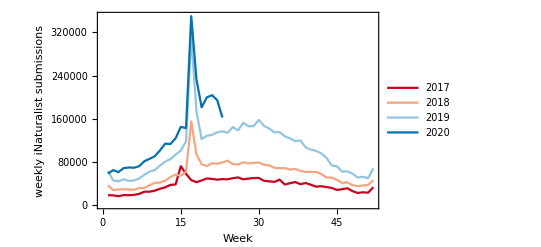

```mathematica
ListLinePlot[Lookup[#,Range[1,52]]&/@Delete[Lookup[Map[Total,GroupBy[(DateValue[#[[1]],"Week"]&)->Last]/@GroupBy[Normal[tsClipped],DateValue[#[[1]],"Year"]&],{2}],Range[2017,2020],<||>],{4,24}],Frame->True,FrameLabel->{"Week","weekly iNaturalist submissions"},PlotLegends->{"2017","2018","2019","2020"},PlotTheme->{"LargeLabels"},PlotStyle->ResourceFunction["ColorBrewerData"]["RdBu",4],PlotRange->All]
```

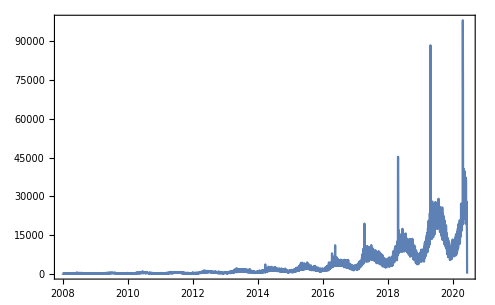

```mathematica
DateListPlot[tsClipped,PlotRange->All]
```

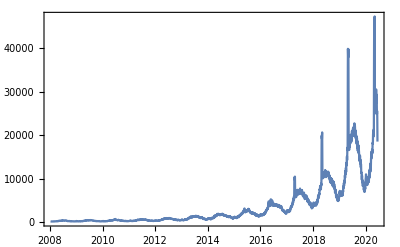

```mathematica
DateListPlot[MovingMap[Mean,tsClipped,Quantity[10, "Days"]],PlotRange->All]
```

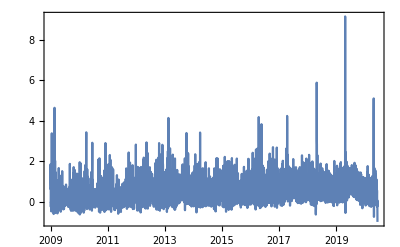

```mathematica
DateListPlot[MovingMap[(Last[#]-First[#])/First[#]&,tsClipped,"Year"],PlotRange->All]
```

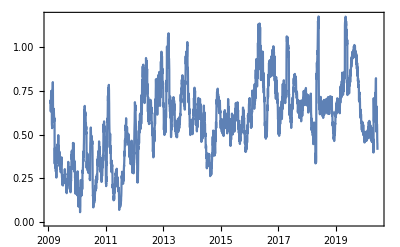

```mathematica
DateListPlot[MovingMap[Mean,MovingMap[(Last[#]-First[#])/First[#]&,tsClipped,"Year"],Quantity[30, "Days"]],PlotRange->All]
```

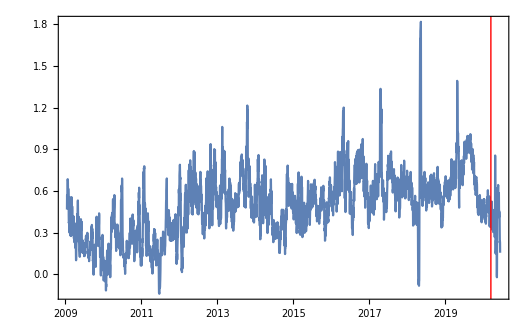

```mathematica
DateListPlot[MovingMap[(Last[#]-First[#])/First[#]&,MovingMap[Mean,tsClipped,Quantity[15, "Days"]],"Year"],Epilog->{Red,InfiniteLine[{DateObject[{2020,3,15}],0},{0,1}]},PlotRange->All]
```

```mathematica
Replace[submitterCountsByMonth
```

```mathematica
Flatten[Table[Table[StringJoin[ToString[x],"-",y],{y,{"01","02","03","04","05","06","07","08","09","10","11","12"}}],{x,2017,2020,1}]]
```

{2017-01,2017-02,2017-03,2017-04,2017-05,2017-06,2017-07,2017-08,2017-09,2017-10,2017-11,2017-12,2018-01,2018-02,2018-03,2018-04,2018-05,2018-06,2018-07,2018-08,2018-09,2018-10,2018-11,2018-12,2019-01,2019-02,2019-03,2019-04,2019-05,2019-06,2019-07,2019-08,2019-09,2019-10,2019-11,2019-12,2020-01,2020-02,2020-03,2020-04,2020-05,2020-06,2020-07,2020-08,2020-09,2020-10,2020-11,2020-12}

```mathematica
submitterCountsByMonth
```

## Weekly

```mathematica
fileStream = OpenRead["/Users/katjad/Documents/iNaturalist/0010107-200613084148143.csv"]
```

InputStream[…]

```mathematica
StreamPosition[fileStream]
```

0

```mathematica
line=ReadLine[fileStream]
```

gbifID	datasetKey	occurrenceID	kingdom	phylum	class	order	family	genus	species	infraspecificEpithet	taxonRank	scientificName	verbatimScientificName	verbatimScientificNameAuthorship	countryCode	locality	stateProvince	occurrenceStatus	individualCount	publishingOrgKey	decimalLatitude	decimalLongitude	coordinateUncertaintyInMeters	coordinatePrecision	elevation	elevationAccuracy	depth	depthAccuracy	eventDate	day	month	year	taxonKey	speciesKey	basisOfRecord	institutionCode	collectionCode	catalogNumber	recordNumber	identifiedBy	dateIdentified	license	rightsHolder	recordedBy	typeStatus	establishmentMeans	lastInterpreted	mediaType	issue

```mathematica
getWeek[do_?DateObjectQ]:=Floor[(UnixTime[do]-UnixTime[DateObject[{DateValue[do,"Year"],1,1}]])/(7*24*60*60)]
```

```mathematica
Now
```

Sun 28 Jun 2020 20:06:26GMT-4.

```mathematica
submitterCountsByWeek = <||>;
recorderCountsByWeek = <||>;
recorderIDs = <||>;
submitterIDs = <||>;
n = 0;
Module[{line,lineList,exactDate,date,recorder, submitter},
	While[line=ReadLine[fileStream];line =!= EndOfFile,
		If[Divisible[n++,100000], Echo[n]];
		lineList = StringSplit[line,"\t"];
		exactDate = DateObject[StringTake[lineList[[30]],10],"Week"];
		date = {DateValue[exactDate,"Year"], getWeek[exactDate]};
		recorder = lineList[[45]];
		submitter = lineList[[41]];
		
		If[
			!KeyExistsQ[recorderIDs,date],
			recorderCountsByWeek[date]=1;
			recorderIDs[date]={recorder},
			If[
				MemberQ[recorderIDs[date],recorder],
				Nothing,
				Append[recorderIDs[date],recorder];
				recorderCountsByWeek[date]++]];
					
		If[
			!KeyExistsQ[submitterIDs,date],
			submitterCountsByWeek[date]=1;
			submitterIDs[date]={recorder},
			If[
				MemberQ[submitterIDs[date],recorder],
				Nothing,
				Append[submitterIDs[date],recorder];
				submitterCountsByWeek[date]++]]
		]
	];
Close[fileStream];
```

```mathematica
16000000/100000
```

160

```mathematica
Now
```

Sun 28 Jun 2020 18:45:20GMT-4.

```mathematica
Dynamic[Column[{n,ProgressIndicator[n,{0,16699363}]}]]
```

```mathematica
(*Export["~/Documents/iNaturalist/submitterCountsByWeek.mx",submitterCountsByWeek];
Export["~/Documents/iNaturalist/recorderCountsByDay.mx",recorderCountsByWeek];*)
```

```mathematica
DateListPlot[submitterCountsByWeek]
```

```mathematica
weekts=TimeSeries[KeySelect[submitterCountsByWeek,DateObjectQ],MissingDataMethod->{"Constant",0}]
```

```mathematica
weekTsClipped=TimeSeriesWindow[weekts,{DateObject[{2008,1,1}],InfiniteFuture}]
```

```mathematica
Normal[weekTsClipped][[;;5]]
```

{{Tue 1 Jan 2008 00:00:00GMT-4.,206},{Wed 2 Jan 2008 00:00:00GMT-4.,82},{Thu 3 Jan 2008 00:00:00GMT-4.,97},{Fri 4 Jan 2008 00:00:00GMT-4.,119},{Sat 5 Jan 2008 00:00:00GMT-4.,128}}

```mathematica
KeySelect[submitterCountsByWeek,DateObjectQ][[;;10]]
```

<|Week beginning: Mon 25 Apr 2011→609,Week beginning: Mon 8 Aug 2011→498,Week beginning: Mon 11 Jan 2010→156,Week beginning: Mon 30 Apr 2012→1025,Week beginning: Mon 28 May 2012→1176,Week beginning: Mon 9 Jul 2012→993,Week beginning: Mon 6 Jul 2009→307,Week beginning: Mon 8 Oct 2012→371,Week beginning: Mon 12 Nov 2012→438,Week beginning: Mon 18 Aug 1980→4|>

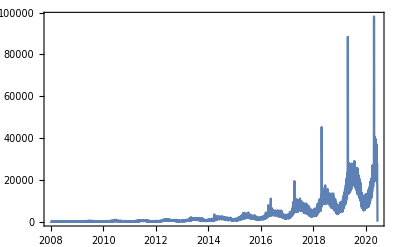

```mathematica
DateListPlot[weekTsClipped,PlotRange->All]
```

```mathematica
Values[GroupBy[Normal[weekTsClipped],DateValue[#[[1]],"Year"]&]][[2]]
```

```mathematica
DateValue[#[[1]],"Week"]&/@Values[GroupBy[Normal[weekTsClipped],DateValue[#[[1]],"Year"]&]][[2]]
```

{1,1,1,1,2,2,2,2,2,2,2,3,3,3,3,3,3,3,4,4,4,4,4,4,4,5,5,5,5,5,5,5,6,6,6,6,6,6,6,7,7,7,7,7,7,7,8,8,8,8,8,8,8,9,9,9,9,9,9,9,10,10,10,10,10,10,10,11,11,11,11,11,11,11,12,12,12,12,12,12,12,13,13,13,13,13,13,13,14,14,14,14,14,14,14,15,15,15,15,15,15,15,16,16,16,16,16,16,16,17,17,17,17,17,17,17,18,18,18,18,18,18,18,19,19,19,19,19,19,19,20,20,20,20,20,20,20,21,21,21,21,21,21,21,22,22,22,22,22,22,22,23,23,23,23,23,23,23,24,24,24,24,24,24,24,25,25,25,25,25,25,25,26,26,26,26,26,26,26,27,27,27,27,27,27,27,28,28,28,28,28,28,28,29,29,29,29,29,29,29,30,30,30,30,30,30,30,31,31,31,31,31,31,31,32,32,32,32,32,32,32,33,33,33,33,33,33,33,34,34,34,34,34,34,34,35,35,35,35,35,35,35,36,36,36,36,36,36,36,37,37,37,37,37,37,37,38,38,38,38,38,38,38,39,39,39,39,39,39,39,40,40,40,40,40,40,40,41,41,41,41,41,41,41,42,42,42,42,42,42,42,43,43,43,43,43,43,43,44,44,44,44,44,44,44,45,45,45,45,45,45,45,46,46,46,46,46,46,46,47,47,47,47,47,47,47,48,48,48,48,48,48,48,49,49,49,49,49,49,49,50,50,50,50,50,50,50,51,51,51,51,51,51,51,52,52,52,52,52,52,52,53,53,53,53}

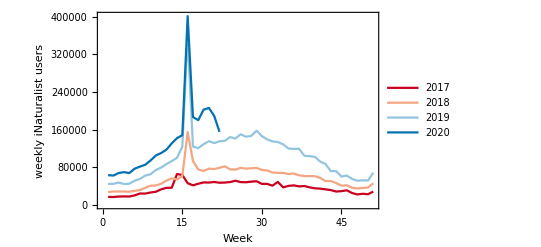

```mathematica
ListLinePlot[Delete[Delete[Delete[Delete[Delete[Lookup[#,Range[1,52]]&/@Lookup[Map[Total,GroupBy[(#[[1]][[2]]&)->Last]/@GroupBy[Normal[submitterCountsByWeek],#[[1]][[1]]&],{2}],Range[2017,2020],<||>],{1,-1}],{2,-1}],{3,-1}],{4,-1}],{4,23}],Frame->True,FrameLabel->{"Week","weekly iNaturalist users"},PlotLegends->{"2017","2018","2019","2020"},PlotTheme->{"LargeLabels"},PlotStyle->ResourceFunction["ColorBrewerData"]["RdBu",4],PlotRange->All]
```